# Signal Convolution

### Consider a continuous, linear and time-invariant (LIT) system whose impulse response h(t) is a rectangular window as shown in Figure 1. For each of the following parts, find the relationship that exists between the initial times and end of the output signal (y(t)) and the signals x(t) and h(t),

Is it possible to establish a relationship between the maximum value of the resulting signal and the amplitude and duration characteristics of the input signal and the impulse response?
According to the activities carried out in this workshop, the LTI system can modify the amplitude and duration characteristics, modifying the signals, whether they are input or output.

a)Select a rectangular window as input signal x(t) (see Figure 1) and observe the signal resulting from the convolution. Move the signal x(t) on the second axis and the resulting signal y(t) will be drawn on the fourth axis.

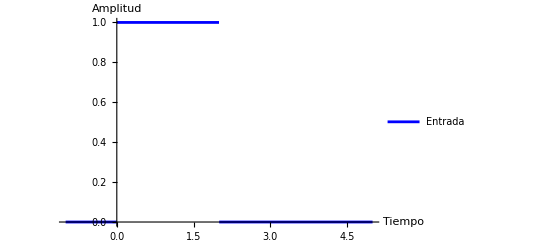

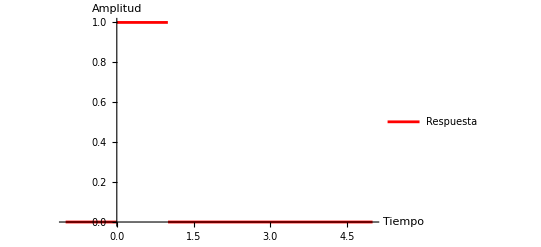

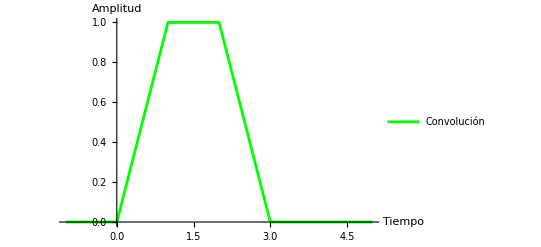

```mathematica
x[t_]:=Piecewise[{{HeavisideTheta[t+1],0<t<2}}](*Señal 1:HeavisideTheta(t-1)*)

h[t_]:=Piecewise[{{HeavisideTheta[t+1],0<t<1}}]; (*Señal 2:HeavisideTheta(t-2)*)

(*Calcular la convolución utilizando Convolve*)
convolution[t_]:=Convolve[x[τ],h[τ],τ,t];

(*Graficar las señales originales y la convolución*)
Plot[{x[t]},{t,-1,5},PlotLegends->{"Entrada"},PlotStyle->{Blue},AxesLabel->{"Tiempo","Amplitud"}]
Plot[{h[t]},{t,-1,5},PlotLegends->{"Respuesta"},PlotStyle->{Red},AxesLabel->{"Tiempo","Amplitud"}]
Plot[{convolution[t]},{t,-1,5},PlotLegends->{"Convolución"},PlotStyle->{Green},AxesLabel->{"Tiempo","Amplitud"}]
```

Select x(t-t0) as the input signal (see figure 2) and observe the signal resulting from the convolution.

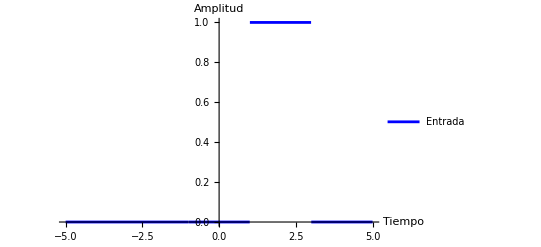

-Graphics-

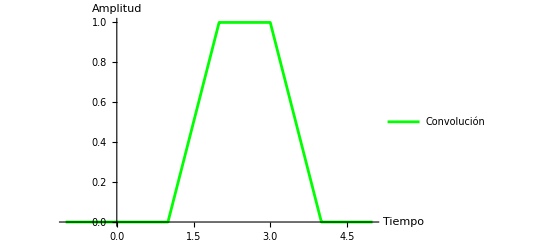

```mathematica
x[t_]:=Piecewise[{{HeavisideTheta[t-1],-1<t<3}}](*Señal 1:HeavisideTheta(t-1)*)

h[t_]:=Piecewise[{{HeavisideTheta[t+1],0<t<1}}]; (*Señal 2:HeavisideTheta(t-2)*)

(*Calcular la convolución utilizando Convolve*)
convolution[t_]:=Convolve[x[τ],h[τ],τ,t];
Plot[{x[t]},{t,-5,5},PlotLegends->{"Entrada"},PlotStyle->{Blue},AxesLabel->{"Tiempo","Amplitud"}]
Plot[{h[t]},{t,-1,5},PlotLegends->{"Respuesta"},PlotStyle->{Red},AxesLabel->{"Tiempo","Amplitud"}]
Plot[{convolution[t]},{t,-1,5},PlotLegends->{"Convolución"},PlotStyle->{Green},AxesLabel->{"Tiempo","Amplitud"}]
```

c) Starting from the signals of the part 
to. increase the width (duration) of some of the windows, and observe the differences with the signal resulting from the convolution with respect to that obtained in the literal

Increasing the input time also increases the output time (the convolution)

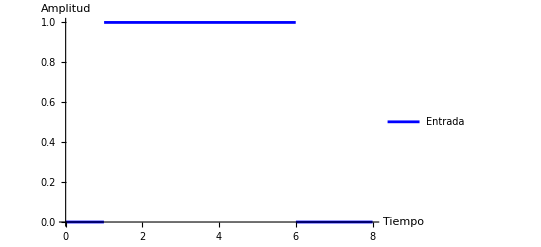

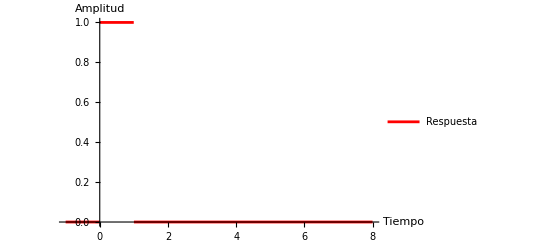

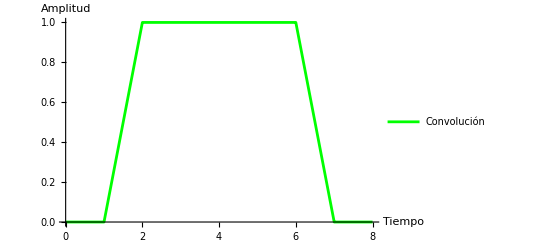

```mathematica
x[t_]:=Piecewise[{{HeavisideTheta[t-1],0<t<6}}](*Señal 1:HeavisideTheta(t-1)*)

h[t_]:=Piecewise[{{HeavisideTheta[t+1],0<t<1}}]; (*Señal 2:HeavisideTheta(t-2)*)

(*Calcular la convolución utilizando Convolve*)
convolution[t_]:=Convolve[x[τ],h[τ],τ,t];
Plot[{x[t]},{t,0,8},PlotLegends->{"Entrada"},PlotStyle->{Blue},AxesLabel->{"Tiempo","Amplitud"}]
Plot[{h[t]},{t,-1,8},PlotLegends->{"Respuesta"},PlotStyle->{Red},AxesLabel->{"Tiempo","Amplitud"}]
Plot[{convolution[t]},{t,0,8},PlotLegends->{"Convolución"},PlotStyle->{Green},AxesLabel->{"Tiempo","Amplitud"}]
```

```mathematica
answer=Convolve[x[τ],h[τ],τ,t]
```

Piecewise[{{7-t, 6<t<7}, {-1+t-(-2+t) HeavisideTheta[-2+t], 1<t≤6}, {0, True}}]

d) Select x(-t-t0) as the input signal and observe the signal resulting from the convolution, establish if it has any relationship with the signal obtained in the previous literal.
Si, se refiere a la convolución anterior, reflejada en el eje y

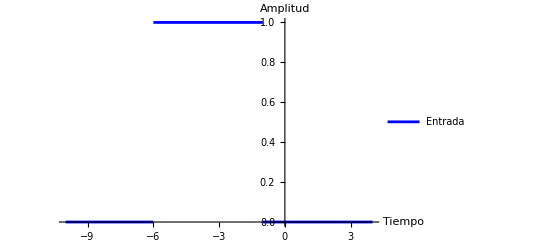

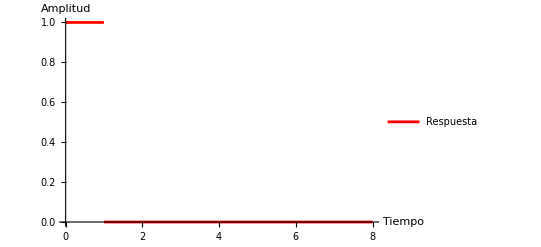

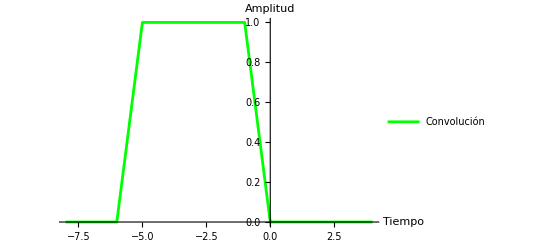

```mathematica
x[t_]:=Piecewise[{{HeavisideTheta[-t-1],-6<t<0}}](*Señal 1:HeavisideTheta(t-1)*)

h[t_]:=Piecewise[{{HeavisideTheta[t+1],0<t<1}}]; (*Señal 2:HeavisideTheta(t-2)*)

(*Calcular la convolución utilizando Convolve*)
convolution[t_]:=Convolve[x[τ],h[τ],τ,t];
Plot[{x[t]},{t,-10,4},PlotLegends->{"Entrada"},PlotStyle->{Blue},AxesLabel->{"Tiempo","Amplitud"}]
Plot[{h[t]},{t,0,8},PlotLegends->{"Respuesta"},PlotStyle->{Red},AxesLabel->{"Tiempo","Amplitud"}]
Plot[{convolution[t]},{t,-8,4},PlotLegends->{"Convolución"},PlotStyle->{Green},AxesLabel->{"Tiempo","Amplitud"}]
```

Select as the input signal the product of a constant a times the signal x(t) of the literal a (see figure 3) and observe the signal resulting from the convolution and compare it with the one obtained in the literal. As seen in the figure below, you can see the scaling of the signal, complying with the linearity property.

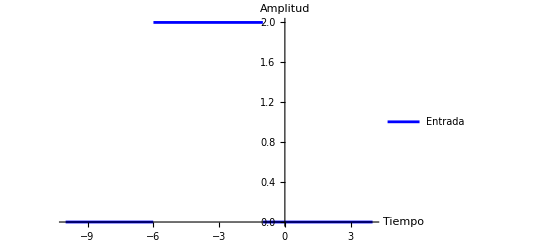

-Graphics-

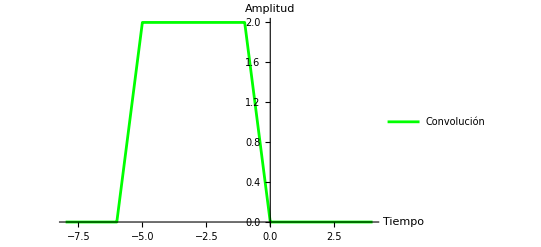

```mathematica
x[t_]:=Piecewise[{{2*HeavisideTheta[-t-1],-6<t<0}}](*Señal 1:HeavisideTheta(t-1)*)

h[t_]:=Piecewise[{{HeavisideTheta[t+1],0<t<1}}]; (*Señal 2:HeavisideTheta(t-2)*)

(*Calcular la convolución utilizando Convolve*)
convolution[t_]:=Convolve[x[τ],h[τ],τ,t];
Plot[{x[t]},{t,-10,4},PlotLegends->{"Entrada"},PlotStyle->{Blue},AxesLabel->{"Tiempo","Amplitud"}]
Plot[{h[t]},{t,0,8},PlotLegends->{"Respuesta"},PlotStyle->{Red},AxesLabel->{"Tiempo","Amplitud"}]
Plot[{convolution[t]},{t,-8,4},PlotLegends->{"Convolución"},PlotStyle->{Green},AxesLabel->{"Tiempo","Amplitud"}]
```

Select as input signal the linear combination of signals: a(x(t))+ x(-t-t0) (see figure 3) and observe the signal resulting from the convolution; verify that the output obtained can be obtained by performing the same linear combination with the outputs obtained in literals a and d. 

Indeed the linearity property is fulfilled as seen in the convolution figure, for two inputs we have two outputs

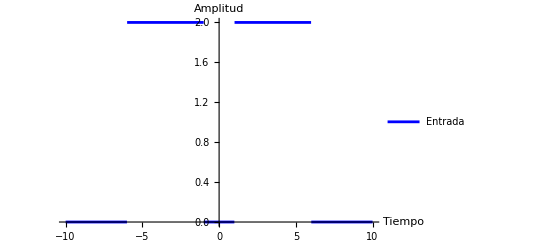

-Graphics-

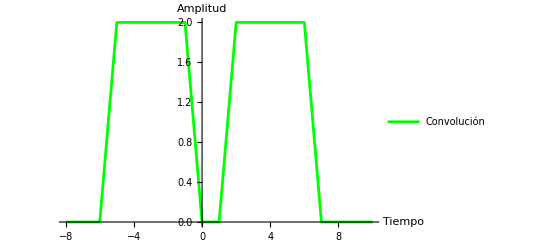

```mathematica
x[t_]:=Piecewise[{{2*HeavisideTheta[t-1],0<t<6}}]+Piecewise[{{2*HeavisideTheta[-t-1],-6<t<0}}](*Señal 1:HeavisideTheta(t-1)*)

h[t_]:=Piecewise[{{HeavisideTheta[t+1],0<t<1}}]; (*Señal 2:HeavisideTheta(t-2)*)

(*Calcular la convolución utilizando Convolve*)
convolution[t_]:=Convolve[x[τ],h[τ],τ,t];
Plot[{x[t]},{t,-10,10},PlotLegends->{"Entrada"},PlotStyle->{Blue},AxesLabel->{"Tiempo","Amplitud"}]
Plot[{h[t]},{t,0,8},PlotLegends->{"Respuesta"},PlotStyle->{Red},AxesLabel->{"Tiempo","Amplitud"}]
Plot[{convolution[t]},{t,-8,10},PlotLegends->{"Convolución"},PlotStyle->{Green},AxesLabel->{"Tiempo","Amplitud"}]
```

What conclusions can you establish from the results obtained from the different convolutions?
carried out?

g) If we have an input signal x(t) and an impulse response h(t), as indicated in figure 4,
How can we obtain the output y(t) from the convolution performed on literal a? Prove your hypothesis. The convolution will be seen as a piecewise function only defined in its intervals with straight lines with negative and positive slopes, there is no constant part because the two signals have the same duration

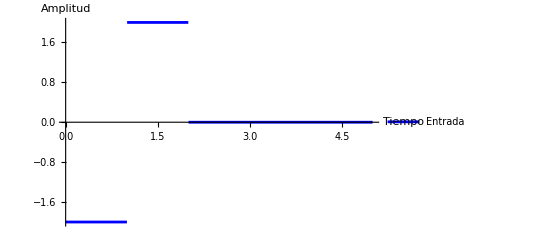

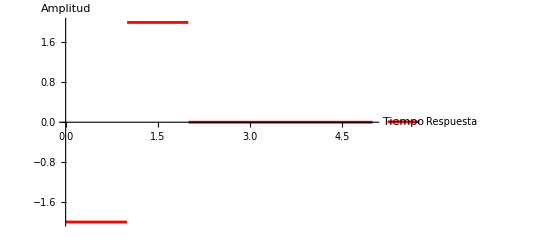

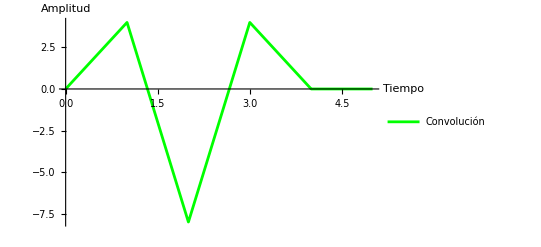

```mathematica
x[t_]:=Piecewise[{{-2*HeavisideTheta[t+1],0<t<1}}]+Piecewise[{{2*HeavisideTheta[t-1],1<t<2}}];(*Señal 1:HeavisideTheta(t-1)*)

h[t_]:=Piecewise[{{-2*HeavisideTheta[t+1],0<t<1}}]+Piecewise[{{2*HeavisideTheta[t-1],1<t<2}}]; (*Señal 2:HeavisideTheta(t-2)*)

(*Calcular la convolución utilizando Convolve*)
convolution[t_]:=Convolve[x[τ],h[τ],τ,t];
Plot[{x[t]},{t,0,5},PlotLegends->{"Entrada"},PlotStyle->{Blue},AxesLabel->{"Tiempo","Amplitud"}]
Plot[{h[t]},{t,0,5},PlotLegends->{"Respuesta"},PlotStyle->{Red},AxesLabel->{"Tiempo","Amplitud"}]
Plot[{convolution[t]},{t,0,5},PlotLegends->{"Convolución"},PlotStyle->{Green},AxesLabel->{"Tiempo","Amplitud"}]
```

```mathematica
Plot[{FourierTransform[h[t],t,w]},{w,-8,10},PlotLegends->{"Convolución"},PlotStyle->{Green},AxesLabel->{"Tiempo","Amplitud"}]
```

h) Analyze the convolution of the two signals in Figure 5, a square window and a decreasing exponential. Into how many intervals can the resulting signal be divided?

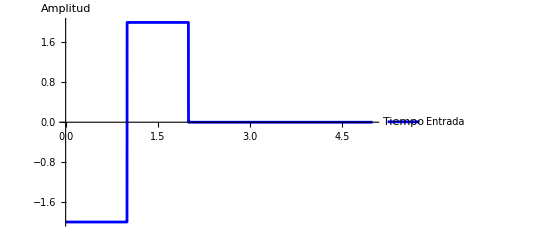

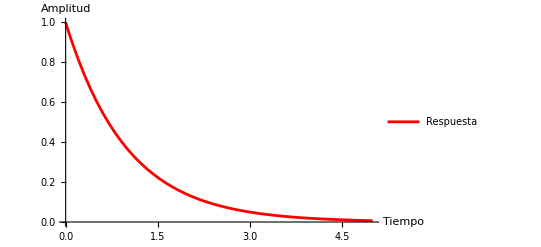

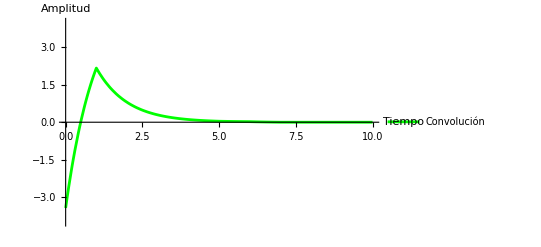

```mathematica
x[t_]:=Piecewise[{{-2*HeavisideTheta[t+1],0<t<1}}]+Piecewise[{{2*HeavisideTheta[t-1],1<t<2}}];(*Señal 1:HeavisideTheta(t-1)*)

h[t_]:=Piecewise[{{Exp[-t],-1<t<5}}] (*Señal 2:HeavisideTheta(t-2)*)


(*Calcular la convolución utilizando Convolve*)
convolution[t_]:=Convolve[x[τ],h[τ],τ,t];
Plot[{x[t]},{t,0,5},PlotLegends->{"Entrada"},PlotStyle->{Blue},AxesLabel->{"Tiempo","Amplitud"}]
Plot[{h[t]},{t,0,5},PlotLegends->{"Respuesta"},PlotStyle->{Red},AxesLabel->{"Tiempo","Amplitud"}]
Plot[{convolution[t]},{t,0,10},PlotRange -> 4,PlotLegends->{"Convolución"},PlotStyle->{Green},AxesLabel->{"Tiempo","Amplitud"}]
```

The signal intervals can be divided into 4, for which the function is formed:Piecewise[{{2 (-1+ⅇ) ⅇ^(1-t), 1<t≤6}, {2 ⅇ (1-ⅇ^-t), 0<t≤1}, {(2 (-1+ⅇ^(7-t)))/ⅇ^5, 6<t<7}, {0, True}}]

```mathematica
answer=Convolve[x[τ],h[τ],τ,t]
```

(Piecewise[{{2 (-1+ⅇ) ⅇ^(1-t), 1<t≤6}, {2 ⅇ (1-ⅇ^-t), 0<t≤1}, {(2 (-1+ⅇ^(7-t)))/ⅇ^5, 6<t<7}, {0, True}}])+(Piecewise[{{-2 (-1+ⅇ) ⅇ^-t, 0<t≤5}, {2/ⅇ^5-2 ⅇ^(1-t), 5<t<6}, {-2 ⅇ+2 ⅇ^-t, -1<t≤0}, {0, True}}])

```mathematica
x[t_]:=Piecewise[{{-1*HeavisideTheta[t+1],-1<t<0}}]+Piecewise[{{1*HeavisideTheta[t],0<t<1}}];
```

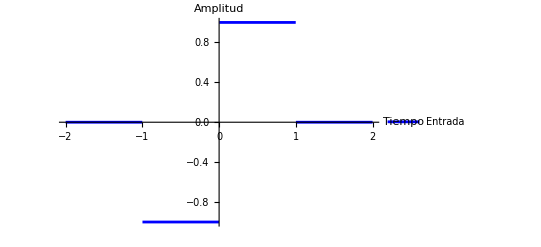

```mathematica
Plot[{x[t]},{t,-2,2},PlotLegends->{"Entrada"},PlotStyle->{Blue},AxesLabel->{"Tiempo","Amplitud"}]
```

```mathematica
h[t_]=∫x[t]ⅆt
```

Piecewise[{{0, t≤-1}, {-((1+t) HeavisideTheta[1+t]), -1<t≤0}, {-1+t HeavisideTheta[t], 0<t≤1}, {0, True}}]

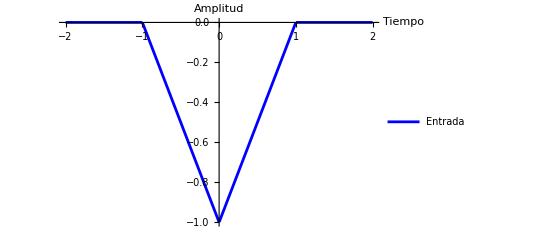

```mathematica
Plot[{h[t]},{t,-2,2},PlotLegends->{"Entrada"},PlotStyle->{Blue},AxesLabel->{"Tiempo","Amplitud"}]
```

```mathematica
g[t_]=-2*h[((1/2)*t)+1/2]
```

-2 (Piecewise[{{0, 1/2+t/2≤-1}, {-((3/2+t/2) HeavisideTheta[3/2+t/2]), -1<1/2+t/2≤0}, {-1+(1/2+t/2) HeavisideTheta[1/2+t/2], 0<1/2+t/2≤1}, {0, True}}])

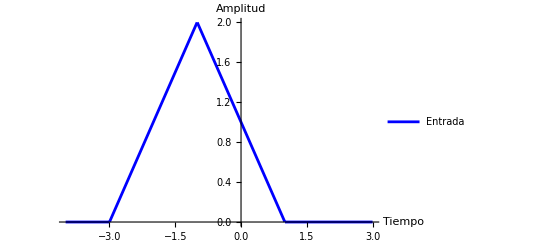

```mathematica
Plot[{g[t]},{t,-4,3},PlotLegends->{"Entrada"},PlotStyle->{Blue},AxesLabel->{"Tiempo","Amplitud"}]
```

-UnitStep[-5+t]+UnitStep[t]

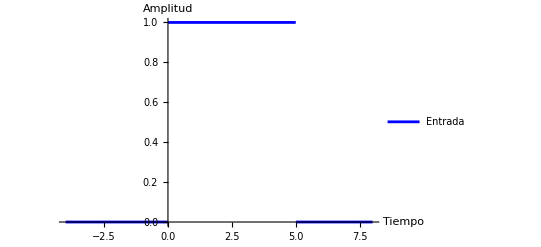

```mathematica
u1[t_]=UnitStep[t]-UnitStep[t-5]
Plot[{u1[t]},{t,-4,8},PlotLegends->{"Entrada"},PlotStyle->{Blue},AxesLabel->{"Tiempo","Amplitud"}]
```

```mathematica
h1[t_]=UnitStep[t-2]-UnitStep[t-8]
```

-UnitStep[-8+t]+UnitStep[-2+t]

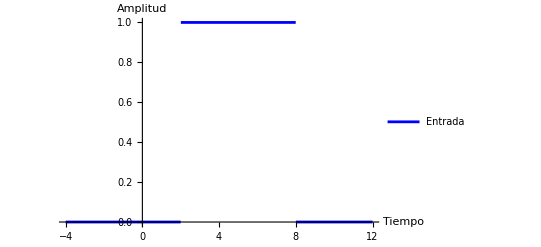

```mathematica
Plot[{h1[t]},{t,-4,12},PlotLegends->{"Entrada"},PlotStyle->{Blue},AxesLabel->{"Tiempo","Amplitud"}]
```

```mathematica
h2[t_]=UnitStep[t-17]-UnitStep[t-11]
```

UnitStep[-17+t]-UnitStep[-11+t]

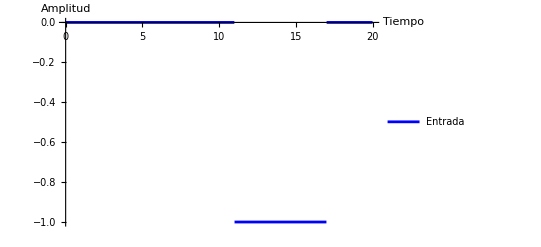

```mathematica
Plot[{h2[t]},{t,0,20},PlotLegends->{"Entrada"},PlotStyle->{Blue},AxesLabel->{"Tiempo","Amplitud"}]
```

```mathematica
uh1[y_]=Convolve[u1[t],h1[t],t,y]
```

(-13+y) UnitStep[-13+y]-(-8+y) UnitStep[-8+y]-(-7+y) UnitStep[-7+y]+(-2+y) UnitStep[-2+y]

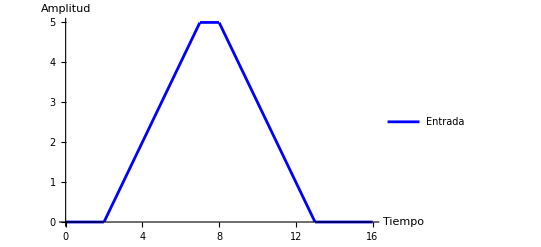

```mathematica
Plot[{uh1[y]},{y,0,16},PlotLegends->{"Entrada"},PlotStyle->{Blue},AxesLabel->{"Tiempo","Amplitud"}]
```

```mathematica
uh2[y_]=Convolve[u1[t],h2[t],t,y]
```

-((-22+y) UnitStep[-22+y])+(-17+y) UnitStep[-17+y]+(-16+y) UnitStep[-16+y]-(-11+y) UnitStep[-11+y]

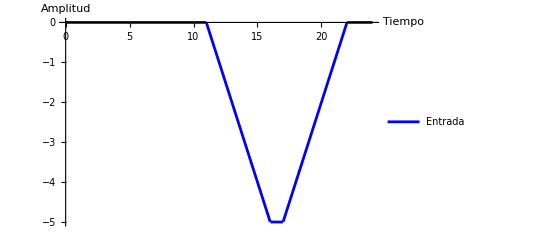

```mathematica
Plot[{uh2[y]},{y,0,24},PlotLegends->{"Entrada"},PlotStyle->{Blue},AxesLabel->{"Tiempo","Amplitud"}]
```

```mathematica
y[t_]=uh1[t]-uh2[t]
```

(-22+t) UnitStep[-22+t]-(-17+t) UnitStep[-17+t]-(-16+t) UnitStep[-16+t]+(-13+t) UnitStep[-13+t]+(-11+t) UnitStep[-11+t]-(-8+t) UnitStep[-8+t]-(-7+t) UnitStep[-7+t]+(-2+t) UnitStep[-2+t]

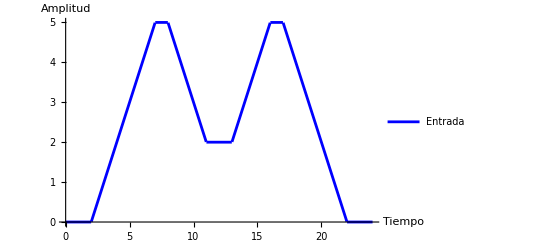

```mathematica
Plot[{y[t]},{t,0,24},PlotLegends->{"Entrada"},PlotStyle->{Blue},AxesLabel->{"Tiempo","Amplitud"}]
```

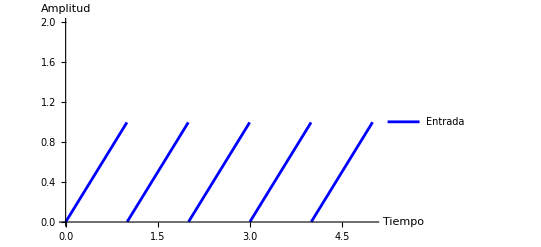

```mathematica
Plot[{SawtoothWave[t]},{t,0,5},PlotLegends->{"Entrada"},PlotStyle->{Blue},AxesLabel->{"Tiempo","Amplitud"},PlotRange->{0,2}]
```

```mathematica
w[t_]=FullSimplify[FourierSeries[SawtoothWave[t],t,20]]
```

$Aborted

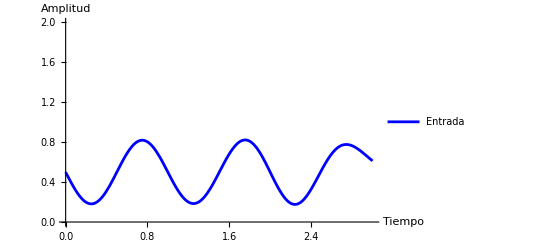

```mathematica
Plot[{w[t]},{t,0,3},PlotLegends->{"Entrada"},PlotStyle->{Blue},AxesLabel->{"Tiempo","Amplitud"},PlotRange->{0,2}]
```

```mathematica
h1[n_]=-1*DiscreteDelta[n]+DiscreteDelta[n-2]
```

DiscreteDelta[-2+n]-DiscreteDelta[n]

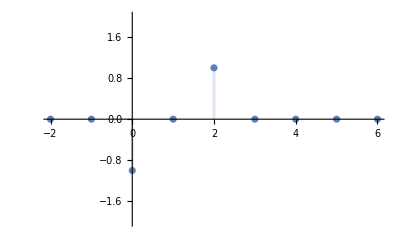

```mathematica
DiscretePlot[h1[n],{n,-2,6},PlotRange->{-2,2}]
```

```mathematica
h2[n_]=-1*UnitStep[DiscreteDelta[n+3]]-UnitStep[DiscreteDelta[n]]
```

-UnitStep[DiscreteDelta[n]]-UnitStep[DiscreteDelta[3+n]]

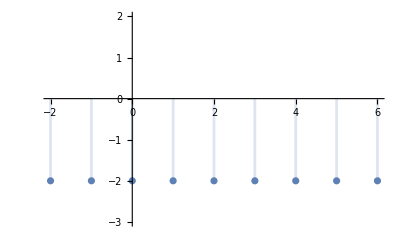

```mathematica
DiscretePlot[h2[n],{n,-2,6},PlotRange->{-3,2}]
```

```mathematica
h3[n_]=UnitStep[DiscreteDelta[n]]
```

UnitStep[DiscreteDelta[n]]

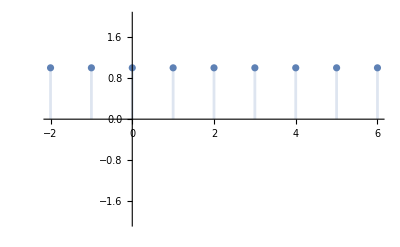

```mathematica
DiscretePlot[h3[n],{n,-2,6},PlotRange->{-2,2}]
```

```mathematica
h4[n_]=DiscreteDelta[n]-DiscreteDelta[n-3]
```

-DiscreteDelta[-3+n]+DiscreteDelta[n]

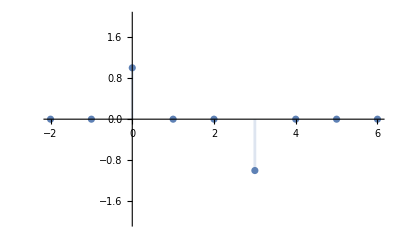

```mathematica
DiscretePlot[h4[n],{n,-2,6},PlotRange->{-2,2}]
```

```mathematica
h1h2[m_]=DiscreteConvolve[h1[n],h2[n],n,m]
```

-2+UnitStep[DiscreteDelta[m]]+UnitStep[DiscreteDelta[3+m]]

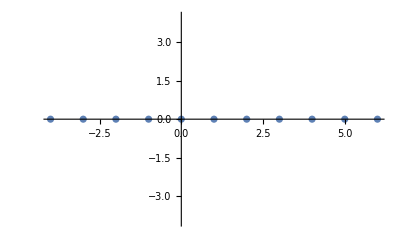

```mathematica
DiscretePlot[h1h2[m],{m,-4,6},PlotRange->{-4,4}]
```

```mathematica
Convolve[-1*DiracDelta[t]+DiracDelta[t-2],-1*UnitStep[t+3]-UnitStep[t],t,n]
```

-UnitStep[-2+n]+UnitStep[n]-UnitStep[1+n]+UnitStep[3+n]

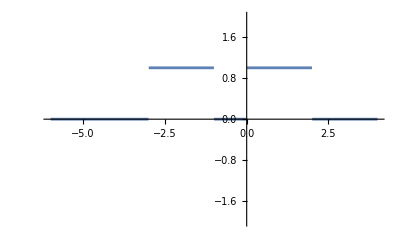

```mathematica
Plot[-UnitStep[-2+n]+UnitStep[n]-UnitStep[1+n]+UnitStep[3+n],{n,-6,4},PlotRange->{-2,2}]
```

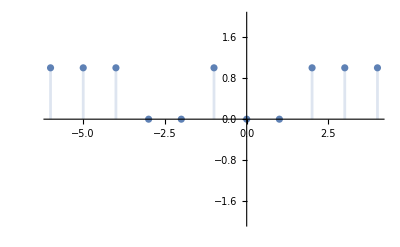

```mathematica
DiscretePlot[DiscreteDelta[-UnitStep[-2+n]+UnitStep[n]-UnitStep[1+n]+UnitStep[3+n]],{n,-6,4},PlotRange->{-2,2}]
```

```mathematica
Convolve[-1*DiracDelta[t]+DiracDelta[t-2],-UnitStep[t],t,n]
```

-UnitStep[-2+n]+UnitStep[n]

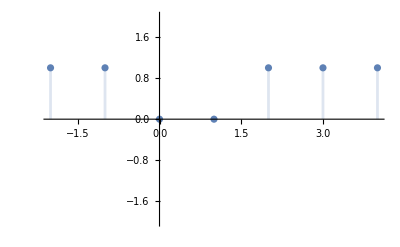

```mathematica
DiscretePlot[DiscreteDelta[-UnitStep[-2+n]+UnitStep[n]],{n,-2,4},PlotRange->{-2,2}]
```

```mathematica
Convolve[-UnitStep[-2+n]+UnitStep[n],DiracDelta[n]-DiracDelta[n-3],n,t]
```

UnitStep[-5+t]-UnitStep[-3+t]-UnitStep[-2+t]+UnitStep[t]

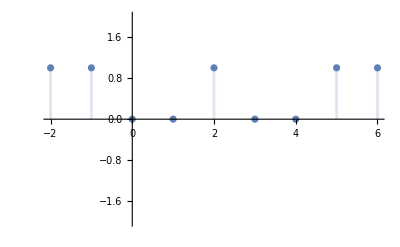

```mathematica
DiscretePlot[DiscreteDelta[UnitStep[-5+t]-UnitStep[-3+t]-UnitStep[-2+t]+UnitStep[t]],{t,-2,6},PlotRange->{-2,2}]
```

```mathematica
DiscreteDelta[UnitStep[-5+t]-UnitStep[-3+t]-UnitStep[-2+t]+UnitStep[t]]+DiscreteDelta[-UnitStep[-2+n]+UnitStep[n]-UnitStep[1+n]+UnitStep[3+n]]
```

DiscreteDelta[-UnitStep[-2+n]+UnitStep[n]-UnitStep[1+n]+UnitStep[3+n]]+DiscreteDelta[UnitStep[-5+t]-UnitStep[-3+t]-UnitStep[-2+t]+UnitStep[t]]

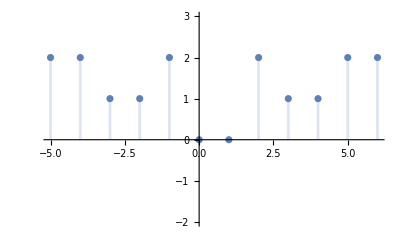

```mathematica
DiscretePlot[DiscreteDelta[-UnitStep[-2+t]+UnitStep[t]-UnitStep[1+t]+UnitStep[3+t]]+DiscreteDelta[UnitStep[-5+t]-UnitStep[-3+t]-UnitStep[-2+t]+UnitStep[t]],{t,-5,6},PlotRange->{-2,3}]
```